# Automatic Researcher

## Description

It’s 2021 and everyone tells you to do your own research. This is obviously absurd because doing research is hard and you’re not going to bother. This project will solve all of your problems by doing research automatically. You can then present a concise, coherent, and comprehensive breakdown of any subject at moment’s notice to win any argument without reading so much as a title. Now go forth and claim that sweet, sweet social credit!

## Basics

Start from keyword

Gather most relevant Wikipedia articles

Present summary

## Goal

Final product: cloud deployed web service

Input: keyword

Output: summary of relevant info and topics in readable form

Bonus: Link tree for important related topics/articles

## Plan

Start from Wikipedia article with title closest to given keyword

Trawl all links recursively to some (lowish) depth and form connectivity tree for topics

Take given number of most relevant articles

Summarize articles

Basic: take top section

Advanced: take sentences with most relevant keywords

After first sentence each major keyword is used, add in summary for relevant article

Continue recursively until depth or length limit is reached

Present information in readable form

## Testing

```mathematica
TextSentences[WikipediaData["research"]][[;;2]]
```

{Research is "creative and systematic work undertaken to increase the stock of knowledge".,It involves the collection, organization, and analysis of information to increase understanding of a topic or issue.}

```mathematica
links=WikipediaData["Research","LinksRules","MaxLevel"->2,"MaxLevelItems"->5];
```

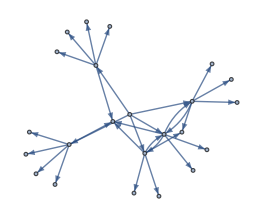

```mathematica
g=Graph[links,VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
CommunityGraphPlot[g]
```

-Graphics-

```mathematica
f=?*Centrality*
```

```mathematica
(* show importance graph and list important articles for all built-in closeness measures *)
Column[Row[{Text@#,showImportance[g,#],o=getOrder[g,#];Column[o[[;;If[Length[o]>10,10,Length[o]]]]]}]&/@{
PageRankCentrality,EigenvectorCentrality,BetweennessCentrality,ClosenessCentrality,LinkRankCentrality,DegreeCentrality,EccentricityCentrality,EdgeBetweennessCentrality,HITSCentrality,KatzCentrality,RadialityCentrality,StatusCentrality
}]
(* pretty broken, PageRankCentrality seems best though *)
```

```mathematica
getLinks[article_,depth_,breadth_]:=WikipediaData[article,
	"LinksRules","MaxLevel"->depth,"MaxLevelItems"->5];
getLinksGraph[links_]:=Graph[links,VertexLabels->Placed["Name",Tooltip]]
showImportance[graph_,func_]:=HighlightGraph[graph,VertexList@graph,
	VertexSize->Thread[VertexList@graph->Rescale[func@graph]],ImageSize->Medium]
getOrder[graph_,func_]:=Part[VertexList[graph],Ordering[func[graph],All,Greater]]
getKeywords[graph_,n_]:=Take[o=getOrder[graph,PageRankCentrality],If[Length[o]>n,n,Length[o]]]
```

```mathematica
showImportance[g,PageRankCentrality]
```

-Graphics-

```mathematica
getOrder[g,PageRankCentrality]
```

{Academia,Academic authorship,Abstract (summary),Academic publishing,Academic journal,Academic ghostwriting,Academic dishonesty,Academic discipline,Academic conference,APA style,Academic,ABC-CLIO,Academic rank,Academic personnel,Academic degree,Aalto University,Abolitionism in the United States,Abigail Thompson,2006 Duke University lacrosse case,14th Amendment to the U.S. Constitution,Academic ranks,Academic freedom,Research}

```mathematica
showImportance[g,EigenvectorCentrality]
```

-Graphics-

```mathematica
getOrder[g,EigenvectorCentrality]
```

{Academic authorship,Academic publishing,Academic journal,Academic rank,Academic personnel,Academic degree,Aalto University,Academic discipline,Academic conference,APA style,Academic,Abstract (summary),ABC-CLIO,Abolitionism in the United States,Abigail Thompson,2006 Duke University lacrosse case,14th Amendment to the U.S. Constitution,Academic ghostwriting,Academic dishonesty,Academia,Academic ranks,Academic freedom,Research}

```mathematica
links=getLinks["Research",2,10];
```

```mathematica
graph=getLinksGraph@links;
```

```mathematica
keywords=getKeywords[graph,5]
```

{Academia,Academic authorship,Abstract (summary),Academic publishing,Academic journal}

```mathematica
fulltext=TextSentences[WikipediaData["Research"]];
```

```mathematica
Map[Function[keyword,keyword->Select[fulltext,StringContainsQ[#,keyword,IgnoreCase->True]&]],keywords]
```

{Academia→{In academia, scholarly peer review is often used to determine an academic paper's suitability for publication.},Academic authorship→{},Abstract (summary)→{},Academic publishing→{Academic publishing is a system that is necessary for academic scholars to peer review the work and make it available for a wider audience.},Academic journal→{The degree of originality of the research is among major criteria for articles to be published in academic journals and usually established by means of peer review.,As the great majority of mainstream academic journals are written in English, multilingual periphery scholars often must translate their work to be accepted to elite Western-dominated journals.,Most established academic fields have their own scientific journals and other outlets for publication, though many academic journals are somewhat interdisciplinary, and publish work from several distinct fields or subfields.}}

## Next

Look for pretrained networks in the Wolfram Neural Net Repository

Keyword extractor

Text summarizer

Text relationships

Correlate keywords with links

Find or build keyword choosing algorithm

Implement TextRank or adapt PageRankCentrality

Dynamically choose parameters for depth and breadth based on length requirement

Build recursion functions for full summaries

Hold link tree for navigation

Build web interface

```mathematica
links=getLinks["Research",2,10];
```

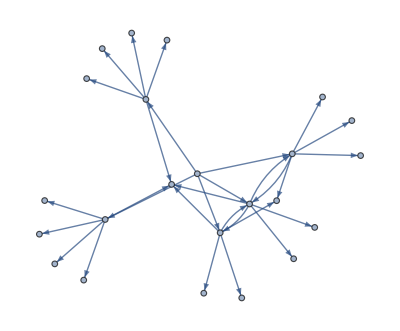

```mathematica
graph=getLinksGraph[links]
```

```mathematica
showImportance[graph,PageRankCentrality]
```

-Graphics-

```mathematica
getKeywords[graph,10]
```

{Academia,Academic authorship,Abstract (summary),Academic publishing,Academic journal,Academic ghostwriting,Academic dishonesty,Academic discipline,Academic conference,APA style}

## TextRank for Keyword Extraction

Filter only nouns and adjectives

Add lexical units to graph

Edge between units that co-occur within a window of N words

Run PageRankCentrality to find top keywords

Find important sentences

Option 1: sentences that contain most keywords

Option 2: run TextRank again for sentences instead

Output top sentences as summary

Find links related to top keywords

Recurse to add summaries

```mathematica
partialtext=fulltext[[1]]
```

Research is "creative and systematic work undertaken to increase the stock of knowledge".

```mathematica
cleanText[text_String]:=StringDelete[text,PunctuationCharacter]//ToLowerCase
```

```mathematica
filterWords[text_String]:=With[{pos=Association@@((#->WordData[#,"PartsOfSpeech"])&/@StringSplit[cleanText[text]])},
Select[Keys[pos],ContainsOnly[pos[#],{"Noun","Adjective"}]&]]
```

```mathematica
filterWords[partialtext]
```

{creative,systematic,collection,organization,analysis,information,understanding,topic,may,expansion,validity,procedures,elements,prior,primary,basic,opposed,applied,are,documentation,discovery,interpretation,development,methods,systems,advancement,human,knowledge}

```mathematica
partialtext=StringJoin[fulltext[[;;5]]]
```

Research is "creative and systematic work undertaken to increase the stock of knowledge".It involves the collection, organization, and analysis of information to increase understanding of a topic or issue.A research project may be an expansion on past work in the field.To test the validity of instruments, procedures, or experiments, research may replicate elements of prior projects or the project as a whole.The primary purposes of basic research (as opposed to applied research) are documentation, discovery, interpretation, and the research and development (R&D) of methods and systems for the advancement of human knowledge.

```mathematica
keywords=filterWords[partialtext]
```

{creative,systematic,collection,organization,analysis,information,understanding,topic,may,expansion,validity,procedures,elements,prior,primary,basic,opposed,applied,are,documentation,discovery,interpretation,development,methods,systems,advancement,human,knowledge}

```mathematica
nextWords[text_,word_,n_]:=With[{words=StringSplit[cleanText[text]],i=Position[words,word][[1,1]]},Take[Rest[words][[i;;UpTo[i+n]]]]]
```

```mathematica
cleanWords=StringSplit@cleanText@partialtext
```

{research,is,creative,and,systematic,work,undertaken,to,increase,the,stock,of,knowledgeit,involves,the,collection,organization,and,analysis,of,information,to,increase,understanding,of,a,topic,or,issue}

```mathematica
Position[cleanWords,"to"]
```

{{8},{22}}

```mathematica
cleanWords[[{1}]]
```

{research}

```mathematica
cleanWords[[{1,2}]]
```

{research,is}

```mathematica
Position[textwords,"project"]
```

{{31},{59}}

```mathematica
textwords=StringSplit[cleanText[partialtext]]
```

{research,is,creative,and,systematic,work,undertaken,to,increase,the,stock,of,knowledgeit,involves,the,collection,organization,and,analysis,of,information,to,increase,understanding,of,a,topic,or,issuea,research,project,may,be,an,expansion,on,past,work,in,the,fieldto,test,the,validity,of,instruments,procedures,or,experiments,research,may,replicate,elements,of,prior,projects,or,the,project,as,a,wholethe,primary,purposes,of,basic,research,as,opposed,to,applied,research,are,documentation,discovery,interpretation,and,the,research,and,development,rd,of,methods,and,systems,for,the,advancement,of,human,knowledge}

```mathematica
Partition[textwords,Min[Length[textwords],5]]
```

{{research,is,creative,and,systematic},{work,undertaken,to,increase,the},{stock,of,knowledgeit,involves,the},{collection,organization,and,analysis,of},{information,to,increase,understanding,of},{a,topic,or,issuea,research},{project,may,be,an,expansion},{on,past,work,in,the},{fieldto,test,the,validity,of},{instruments,procedures,or,experiments,research},{may,replicate,elements,of,prior},{projects,or,the,project,as},{a,wholethe,primary,purposes,of},{basic,research,as,opposed,to},{applied,research,are,documentation,discovery},{interpretation,and,the,research,and},{development,rd,of,methods,and},{systems,for,the,advancement,of}}

```mathematica
wordlist=First@%175
```

{research,is,creative,and,systematic}

```mathematica
linkAllKeywords[wordlist_,keywords_]:=Flatten[Function[word,If[MemberQ[keywords,#]&&word!=#,word->#,Nothing]&/@wordlist]/@Select[wordlist,MemberQ[keywords,#]&]]
```

```mathematica
localKeywordLinks[wordlist_,keywords_,distance_]:=
Flatten[linkAllKeywords[#,keywords]&/@Partition[wordlist,Min[Length[wordlist],distance]]]//Function[DeleteCases[#,{}]]
```

```mathematica
localKeywordLinks[textwords,keywords,5]
```

{}

```mathematica
keywords=WikipediaData["Research","LinksList"]
```

## Revised Method

Get Article Summary:

Find most important keywords using PageRankCentrality of all article links

Find most important sentences using PageRankCentrality of sentence relations

For each important sentence that contains an important link, splice in article summary of link

Recursively combine article summaries down to given level

## Get Important Sentences

```mathematica
sentenceSimilarity[s1_,s2_]:=With[{c1=getWords[s1],c2=getWords[s2]},
Length[Intersection[c1,c2]]/(Log[Length[c1]]+Log[Length[c2]])]//N
```

```mathematica
(* get article key sentences *)
getWords[text_]:=StringDelete[text,PunctuationCharacter]//ToLowerCase//StringSplit
filterWords[words_]:=With[{pos=Association@@((#->WordData[#,"PartsOfSpeech"])&/@words)},
	Select[Keys[pos],ContainsAny[pos[#],{"Noun","Adjective"}]&&ContainsNone[pos[#],{"Preposition","Determiner"}]&]]
sentenceSimilarity[s1_,s2_,keywords_]:=With[{
	c1=Intersection[getWords[s1],keywords],c2=Intersection[getWords[s2],keywords]},
	Length[Intersection[c1,c2]]/(Log[Length[c1]]+Log[Length[c2]]+.0000001)]//N
```

```mathematica
sentences=TextSentences[WikipediaData["Research"]];
```

```mathematica
sentences[[1]]
```

Research is "creative and systematic work undertaken to increase the stock of knowledge".

```mathematica
getWords[sentences[[1]]]
```

{research,is,creative,and,systematic,work,undertaken,to,increase,the,stock,of,knowledge}

```mathematica
sentences[[2]]
```

It involves the collection, organization, and analysis of information to increase understanding of a topic or issue.

```mathematica
keywords=filterWords[getWords[WikipediaData["Research"]]];
```

```mathematica
sentenceSimilarity[#[[1]],#[[2]],keywords]&/@Tuples[sentences[[;;3]],2]
```

{1.79864,0.248425,0.535093,0.248425,1.92359,0.,0.535093,0.,1.67433}

## Weights for PageRankCentrality

Form all connections between sentences

Get vertex list of graph for ordering

For each sentence, calculate initial centrality as sum of similarity to all other sentences

```mathematica
getInitialWeight[sentence_,sentences_,keywords_]:=Total[sentenceSimilarity[sentence,#,keywords]&/@DeleteCases[sentences,sentence]]
```

```mathematica
getInitialWeight[#,sentences,keywords]&/@sentences
```

{44.4882,9.76507,47.8142,39.0404,49.6267,42.4506,50.9674,48.753,0.,33.358,2.4089,0.,47.0267,45.9295,11.7757,34.207,55.2564,40.6335,0.,44.3148,43.7875,8.67215,21.9099,13.7196,40.3271,46.597,49.0929,43.1122,1.01914,38.1354,48.4397,41.392,45.4319,7.21126,8.3144,44.1484,9.73014,3.41343,19.7697,52.4795,46.2565,60.0296,43.8403,51.8799,38.6929,9.28193,2.89869,45.294,6.07311,1.74426,5.50762,45.8573,12.8486,8.21032,13.4135,7.03284,12.6697,8.07064,6.07017,13.2676,13.2277,6.76257,11.13,8.39194,14.537,55.3761,41.209,17.3041,0.279055,53.2638,8.76176,57.2887,37.7977,46.7292,40.8888,40.9543,9.8118,1.06433,44.6327,40.3916,41.8822,38.9577,40.1419,47.0204,41.3619,40.2558,32.2301,1.79082,6.54821,14.978,53.8116,48.001,42.7007,39.9768,52.9984,42.0727,40.7744,41.6443,43.5886,44.0558,51.4992,4.76977,15.3342,51.6989,23.8303,47.3273,41.2904,48.7279,4.91901,58.9089,15.7658,61.2403,45.346,8.61872,43.4533,40.9263,40.8705,53.0188,47.4384,44.3822,0.603096,38.2764,39.9176,44.918,41.6768,54.4297,48.4613,47.6867,43.3169,42.324,16.0615,29.8599,37.5407,49.3851,16.4867,37.6191,56.1821,46.1019,52.4925,45.2823,49.4517,5.37556,17.8881,48.6561,45.4745,44.947,41.8484,41.1227,42.7676,8.6261,45.3412,4.8823,49.3919,10.8425,22.575,43.9243,42.5746,56.2277,40.5653,40.7026,41.7877,39.9905,10.3758,42.8892,42.6111,9.16003,37.5041,43.6353,40.7422,44.2813,53.9012,0.,53.0474,40.1058,1.44696,1.68023,39.5214,61.2403,54.7289,31.9358,20.5155,55.2258,3.33432,0.892821,46.2451,40.6668,17.5165,5.95007,18.6502,8.68076,15.6677,15.5621,15.1154,0.,6.4383,14.3764,18.3977,7.0001,7.10721,8.02448,19.7073,10.9088,15.8356,14.1564,5.52769,37.0056,0.660634,4.80046,7.17709,5.1402,8.06527,15.6544,0.45512,21.1526,0.613523,37.5416,3.9348,39.189,35.7035,42.2677,1.85783,0.45512,38.3668,0.,37.8049,14.0776,47.2028,51.7161,44.7014,47.2028,1.57297,12.6857,2.07748,8.497,40.9421,42.5632,5.03643,24.0638,47.5274,17.0806,5.68226,13.1756,2.34695,4.186,19.7982,55.1119,37.6427,11.3094,37.4235,47.6302,4.28688,2.44349,0.,1.01448,0.,48.9607,3.85194,0.,0.,0.,37.2064,40.0331,0.,0.,0.,0.,48.7326,0.,5.26704,0.314658}

```mathematica
weights=%68;
```

```mathematica
Part[sentences,OrderingBy[sentences,weights[[Position[sentences,#][[1,1]]]]&]]
```

{2014.,Arieli, T. (2011).,Cohen, N.;,== Definitions ==,doi:10.1177/0022343311405698.,== Etymology ==,=== Generalizability ===,Groh, Arnold (2018).,=== In Russia ===,ISBN 978-3-319-72774-5.,=== Meta-research ===,== References ==,S2CID 145328311.,Soeters, Joseph; Shields, Patricia and Rietjens, Sebastiaan.,Talja, Sanna and Pamela J. Mckenzie (2007).,This material is of a primary-source character.,This includes lower criticism and sensual criticism.,== External links ==,== Professionalisation ==,=== Reseach teams ===,that is analyzed, and searching for themes.,=== Future perspectives ===,=== Influence of the open-access movement ===,=== Bias ===,== Further reading ==,It makes practical applications possible.,Through presented documentation, the insights gained shall be placed in a context.",Meta-research concerns itself with the detection of bias, methodological flaws, and other errors and inefficiencies.,== Publishing ==,Among the finding of meta-research is a low rates of reproducibility across a large number of fields.,Conceptual definition: Description of a concept by relating it to other concepts.,In 2016, the European League of Institutes of the Arts launched The Florence Principles' on the Doctorate in the Arts.,=== Neo-colonial approaches ===,The system varies widely by field and is also always changing, if often slowly.,Since about the early 1990s, licensing of electronic resources, particularly journals, has been very common.,The earliest recorded use of the term was in 1577.,== See also ==,A keen interest in the chosen subject area is advisable.,For example, "Hua Oranga" was created as a criterion for psychological evaluation in Māori populations, and is based on dimensions of mental health important to the Māori people – "taha wairua (the spiritual dimension), taha hinengaro (the mental dimension), taha tinana (the physical dimension), and taha whanau (the family dimension)".,Other studies aim to merely examine the occurrence of behaviours in societies and communities, without particularly looking for reasons or motivations to explain these.,New York: Springer.,Marginson argues that the East Asian Confucian model could take over the Western model.,Presently, a major trend, particularly with respect to scholarly journals, is open access.,The Social Psychology Network provides a comprehensive list of U.S. Government and private foundation funding sources.,The hypothesis is the supposition to be tested.,The open access movement assumes that all information generally deemed useful should be free and belongs to a "public domain", that of "humanity".,Neither one is less effective than the other since they have their particular purpose in science.,Rudolph Rummel says, "... no researcher should accept any one or two tests as definitive.,In publishing, STM publishing is an abbreviation for academic publications in science, technology, and medicine.,For instance, most indigenous communities consider that access to certain information proper to the group should be determined by relationships.,Editor's Introduction: Special Issue on Discursive Approaches to Information Seeking in Context, The University of Chicago Press.,This method has benefits that using one method alone cannot offer.,Operational definition: Details in regards to defining the variables and how they will be measured/assessed in the study.,It was observed that publications from periphery countries rarely rise to the same elite status as those of North America and Europe, because limitations on the availability of resources including high-quality paper and sophisticated image-rendering software and printing tools render these publications less able to satisfy standards currently carrying formal or informal authority in the publishing industry.,It has also been suggested that all published studies should be subjected to some measure for assessing the validity or reliability of its procedures to prevent the publication of unproven findings.,Multilingual scholars' influences from their native communicative styles can be assumed to be incompetence instead of difference.,However, if the outcome is consistent with the hypothesis, the experiment is said to support the hypothesis.,Hypothesis: A testable prediction which designates the relationship between two or more variables.,Generalization is the process of more broadly applying the valid results of one study.,The Florence Principles relating to the Salzburg Principles and the Salzburg Recommendations of the European University Association name seven points of attention to specify the Doctorate / PhD in the Arts compared to a scientific doctorate / PhD.,A useful hypothesis allows prediction and within the accuracy of observation of the time, the prediction will be verified.,Despite the issue of generalizability, single-country studies have risen in prevalence since the late 2000s.,Test, revising of hypothesis
Conclusion, reiteration if necessaryA common misconception is that a hypothesis will be proven (see, rather, null hypothesis).,=== Publication peer review ===,This idea gained prevalence as a result of Western colonial history and ignores alternative conceptions of knowledge circulation.,Humanities scholars usually do not search for the ultimate correct answer to a question, but instead, explore the issues and details that surround it.,Peer review is a form of self-regulation by qualified members of a profession within the relevant field.,There is alleged to be a double standard in the Western knowledge system.,If the outcome is inconsistent with the hypothesis, then the hypothesis is rejected (see falsifiability).,Analysis of data: Involves breaking down the individual pieces of data to draw conclusions about it.,Context is always important, and context can be social, historical, political, cultural, or ethnic.,In this case, a new hypothesis will arise to challenge the old, and to the extent that the new hypothesis makes more accurate predictions than the old, the new will supplant it.,Most academic work is published in journal article or book form.,This process takes three main forms (although, as previously discussed, the boundaries between them may be obscure):,This, however, does not mean that new ideas and innovations cannot be found within the pool of existing and established knowledge.,In experimental work, it typically involves direct or indirect observation of the researched subject(s), e.g., in the laboratory or in the field, documents the methodology, results, and conclusions of an experiment or set of experiments, or offers a novel interpretation of previous results.,Since 2000, Latin American countries have become more popular in single-country studies.,Identification of origin date
Evidence of localization
Recognition of authorship
Analysis of data
Identification of integrity
Attribution of credibility,There may also be consequences for the environment, for society or for future generations that need to be considered.,The subject area should not be randomly chosen since it requires reading a vast amount of literature on the topic to determine the gap in the literature the researcher intends to narrow.,Historians use primary sources and other evidence to systematically investigate a topic, and then to write histories in the form of accounts of the past.,It involves the collection, organization, and analysis of information to increase understanding of a topic or issue.,It is based on artistic practices, methods, and criticality.,When making ethical decisions, we may be guided by different things and philosophers commonly distinguish between approaches like deontology, consequentialism, virtue ethics and value (ethics).,See Scientific method.,In academia, scholarly peer review is often used to determine an academic paper's suitability for publication.,As the accuracy of observation improves with time, the hypothesis may no longer provide an accurate prediction.,These are managed primarily through universities and in some cases through military contractors.,It consists of three steps: pose a question, collect data to answer the question, and present an answer to the question.,Generally, a hypothesis is used to make predictions that can be tested by observing the outcome of an experiment.,Academic publishing is a system that is necessary for academic scholars to peer review the work and make it available for a wider audience.,The instruments used for data collection must be valid and reliable.,Business models are different in the electronic environment.,In this sense, a hypothesis can never be proven, but rather only supported by surviving rounds of scientific testing and, eventually, becoming widely thought of as true.,This careful language is used because researchers recognize that alternative hypotheses may also be consistent with the observations.,Data Interpretation: This can be represented through tables, figures, and pictures, and then described in words.,In some subjects which do not typically carry out experimentation or analysis of this kind, the originality is in the particular way existing understanding is changed or re-interpreted based on the outcome of the work of the researcher.,The following ranks are known:,The tradition of peer reviews being done for free has however brought many pitfalls which are also indicative of why most peer reviewers decline many invitations to review.,Studies with a narrow scope can result in a lack of generalizability, meaning that the results may not be applicable to other populations or regions.,Researchers can also use a null hypothesis, which states no relationship or difference between the independent or dependent variables.,The Florence Principles have been endorsed and are supported also by AEC, CILECT, CUMULUS and SAR.,Within Africa, English-speaking countries are more represented than other countries.,The researcher(s) collects data to test the hypothesis.,Patterns of geographic bias also show a relationship with linguicism: countries whose official languages are French or Arabic are far less likely to be the focus of single-country studies than countries with different official languages.,On the one hand, "digital right management" used to restrict access to personal information on social networking platforms is celebrated as a protection of privacy, while simultaneously when similar functions are used by cultural groups (i.e. indigenous communities) this is denounced as "access control" and reprehended as censorship.,In contrast, countries in Oceania and the Caribbean are the focus of very few studies.,[i.e., you have already found it] If you don't know what you're searching for, what are you searching for?!",Usually, the peer review process involves experts in the same field who are consulted by editors to give a review of the scholarly works produced by a colleague of theirs from an unbiased and impartial point of view, and this is usually done free of charge.,The quantitative data collection methods rely on random sampling and structured data collection instruments that fit diverse experiences into predetermined response categories.,If this is not feasible, the researcher may collect data on participant and situational characteristics to statistically control for their influence on the dependent, or outcome, variable.,A study suggests that researchers should not give great consideration to findings that are not replicated frequently.,There are various history guidelines that are commonly used by historians in their work, under the headings of external criticism, internal criticism, and synthesis.,As the great majority of mainstream academic journals are written in English, multilingual periphery scholars often must translate their work to be accepted to elite Western-dominated journals.,For example, a researcher may choose to conduct a qualitative study and follow it up with a quantitative study to gain additional insights.,In comparative politics, this can result from using a single-country study, rather than a study design that uses data from multiple countries.,For comparative politics, Western countries are over-represented in single-country studies, with heavy emphasis on Western Europe, Canada, Australia, and New Zealand.,Peer review methods are employed to maintain standards of quality, improve performance, and provide credibility.,These studies may be qualitative or quantitative, and can use a variety of approaches, such as queer theory or feminist theory.,There are two main forms of open access: open access publishing, in which the articles or the whole journal is freely available from the time of publication, and self-archiving, where the author makes a copy of their own work freely available on the web.,The increasing participation of indigenous peoples as researchers has brought increased attention to the scientific lacuna in culturally-sensitive methods of data collection.,Indications that fresh (new) teams are associated with more original and more multidisciplinary  scientific studies has been found by An Zeng et al.,In analytical work, there are typically some new (for example) mathematical results produced, or a new way of approaching an existing problem.,A simple example of a non-empirical task is the prototyping of a new drug using a differentiated application of existing knowledge; another is the development of a business process in the form of a flow chart and texts where all the ingredients are from established knowledge.,The results of the data analysis in rejecting or failing to reject the null hypothesis are then reported and evaluated.,Most established academic fields have their own scientific journals and other outlets for publication, though many academic journals are somewhat interdisciplinary, and publish work from several distinct fields or subfields.,These methods produce results that can be summarized, compared, and generalized to larger populations if the data are collected using proper sampling and data collection strategies.,Researchers are overwhelmingly taught Western methods of data collection and study.,Patricia Leavy addresses eight arts-based research (ABR) genres: narrative inquiry, fiction-based research, poetry, music, dance, theatre, film, and visual art.,The word research is derived from the Middle French "recherche", which means "to go about seeking", the term itself being derived from the Old French term "recerchier" a compound word from "re-" + "cerchier", or "sercher", meaning 'search'.,The Merriam-Webster Online Dictionary defines research in more detail as "studious inquiry or examination; especially : investigation or experimentation aimed at the discovery and interpretation of facts, revision of accepted theories or laws in the light of new facts, or practical application of such new or revised theories or laws",Focussed on emphasizing educational achievement, East Asian cultures, mainly in China and South Korea, have encouraged the increase of funding for research expansion.,These limitations in turn result in the under-representation of scholars from periphery nations among the set of publications holding prestige status relative to the quantity and quality of those scholars' research efforts, and this under-representation in turn results in disproportionately reduced acceptance of the results of their efforts as contributions to the body of knowledge available worldwide.,"Field research in conflict environments: Methodological challenges and snowball sampling".,Many senior researchers (such as group leaders) spend a significant amount of their time applying for grants for research funds.,Research ethics is most developed as a concept in medical research, the most notable Code being the 1964 Declaration of Helsinki.,Quantitative research is concerned with testing hypotheses derived from theory or being able to estimate the size of a phenomenon of interest.,Even though Western dominance seems to be prominent in research, some scholars, such as Simon Marginson, argue for "the need [for] a plural university world".,If the intent is to generalize from the research participants to a larger population, the researcher will employ probability sampling to select participants.,Most funding for scientific research comes from three major sources: corporate research and development departments; private foundations, for example, the Bill and Melinda Gates Foundation; and government research councils such as the National Institutes of Health in the USA and the Medical Research Council in the UK.,The controversial trend of artistic teaching becoming more academics-oriented is leading to artistic research being accepted as the primary mode of enquiry in art as in the case of other disciplines.,In present-day Russia, the former Soviet Union and in some post-Soviet states the term researcher (Russian: Научный сотрудник, nauchny sotrudnik) is both a generic term for a person who carried out scientific research, as well as a job position within the frameworks of the USSR Academy of Sciences, Soviet universities, and in other research-oriented establishments.,Scientific research is funded by public authorities, by charitable organizations and by private groups, including many companies.,This type of research aims to investigate a question without attempting to quantifiably measure variables or look to potential relationships between variables.,In several national and private academic systems, the professionalisation of research has resulted in formal job titles.,Observations and formation of the topic: Consists of the subject area of one's interest and following that subject area to conduct subject-related research.,According to artist Hakan Topal, in artistic research, "perhaps more so than other disciplines, intuition is utilized as a method to identify a wide range of new and unexpected productive modalities".,To test the validity of instruments, procedures, or experiments, research may replicate elements of prior projects or the project as a whole.,This could be due to changes in funding for research both in the East and the West.,This widespread difficulty in reproducing research has been termed the "replication crisis.",It is viewed as more restrictive in testing hypotheses because it can be expensive and time-consuming and typically limited to a single set of research subjects.,The hourglass model starts with a broad spectrum for research, focusing in on the required information through the method of the project (like the neck of the hourglass), then expands the research in the form of discussion and results.,Informed consent is a key concept in research ethics.,Journal of Peace Research. 48 (4): 423–436.,Also known as "research on research", it aims to reduce waste and increase the quality of research in all fields.,Most writers, whether of fiction or non-fiction books, also have to do research to support their creative work.,The Society for Artistic Research (SAR) publishes the triannual Journal for Artistic Research (JAR), an international, online, open access, and peer-reviewed journal for the identification, publication, and dissemination of artistic research and its methodologies, from all arts disciplines and it runs the Research Catalogue (RC), a searchable, documentary database of artistic research, to which anyone can contribute.,The degree of originality of the research is among major criteria for articles to be published in academic journals and usually established by means of peer review.,A simpler understanding by Julian Klein defines artistic research as any kind of research employing the artistic mode of perception.,Research ethics is concerned with the moral issues that arise during or as a result of research activities, as well as the ethical conduct of researchers.,Original research, also called primary research, is research that is not exclusively based on a summary, review, or synthesis of earlier publications on the subject of research.,Periphery scholars face the challenges of exclusion and linguicism in research and academic publication.,Historically, the revelation of scandals such as Nazi human experimentation and the Tuskegee syphilis experiment led to the realisation that clear measures are needed for the ethical governance of research to ensure that people, animals and environments are not unduly harmed in research.,In countries such as Canada, mandatory research ethics training is required for students, professors and others who work in research.,Most research begins with a general statement of the problem, or rather, the purpose for engaging in the study.,Empirical research, which tests the feasibility of a solution using empirical evidence.,As such, it is similar to the social sciences in using qualitative research and intersubjectivity as tools to apply measurement and critical analysis.,Constructive research, which tests theories and proposes solutions to a problem or question.,There is also a large body of research that exists in either a thesis or dissertation form.,Artistic research has been defined by the School of Dance and Circus (Dans och Cirkushögskolan, DOCH), Stockholm in the following manner – "Artistic research is to investigate and test with the purpose of gaining knowledge within and for our artistic disciplines.,Non-empirical researchNon-empirical (theoretical) research is an approach that involves the development of theory as opposed to using observation and experimentation.,The historical method comprises the techniques and guidelines by which historians use historical sources and other evidence to research and then to write history.,However, some researchers advocate for the reverse approach: starting with articulating findings and discussion of them, moving "up" to identification of a research problem that emerges in the findings and literature review.,Background research could include, for example, geographical or procedural research.,Scientific research is a widely used criterion for judging the standing of an academic institution, but some argue that such is an inaccurate assessment of the institution, because the quality of research does not tell about the quality of teaching (these do not necessarily correlate).,The literature review identifies flaws or holes in previous research which provides justification for the study.,Qualitative research is linked with the philosophical and theoretical stance of social constructionism.,The management of research ethics is inconsistent across countries and there is no universally accepted approach to how it should be addressed.,Correlation Research Method 
Switching topicsThere have been indications that during the last decades scientists have switched  between scientific  topics more frequently.,For a survey of the central problematics of today's artistic research, see Giaco Schiesser.,Data collection
Verifying data
Analyzing and interpreting the data
Reporting and evaluating research
Communicating the research findings and, possibly, recommendationsThe steps generally represent the overall process; however, they should be viewed as an ever-changing iterative process rather than a fixed set of steps.,In contrast, in the Western academic world, notably in the United Kingdom as well as in some state governments in the United States, funding cuts for university research have occurred, which some say may lead to the future decline of Western dominance in research.,Quantitative research is linked with the philosophical and theoretical stance of positivism.,Approaches to research depend on epistemologies, which vary considerably both within and between humanities and sciences.,These forms of research can be found in databases explicitly for theses and dissertations.,Mathematics research does not rely on externally available data; rather, it seeks to prove theorems about mathematical objects.,Ethical issues may arise in the design and implementation of research involving human experimentation or animal experimentation.,Research is often conducted using the hourglass model structure of research.,As such, non-empirical research seeks solutions to problems using existing knowledge as its source.,Regardless of approach, the application of ethical theory to specific controversial topics is known as applied ethics and research ethics can be viewed as a form of applied ethics because ethical theory is applied in real-world research scenarios.,This research provides scientific information and theories for the explanation of the nature and the properties of the world.,Statistics derived from quantitative research can be used to establish the existence of associative or causal relationships between variables.,Exploratory research, which helps to identify and define a problem or question.,Often, a literature review is conducted in a given subject area before a research question is identified.,Research in other fields such as social sciences, information technology, biotechnology, or engineering may generate different types of ethical concerns to those in medical research.,Original research can take a number of forms, depending on the discipline it pertains to.,Generally, research is understood to follow a certain structural process.,Much of cosmological research is theoretical in nature.,A gap in the current literature, as identified by a researcher, then engenders a research question.,An example of research in the humanities is historical research, which is embodied in historical method.,Nowadays, research ethics is commonly distinguished from matters of research integrity that includes issues such as scientific misconduct (e.g. fraud, fabrication of data or plagiarism).,The purpose of the original research is to produce new knowledge, rather than to present the existing knowledge in a new form (e.g., summarized or classified).,Qualitative research
This involves understanding human behavior and the reasons that govern such behavior, by asking a broad question, collecting data in the form of words, images, video etc.,Research is "creative and systematic work undertaken to increase the stock of knowledge".,Artistic research aims to enhance knowledge and understanding with presentation of the arts.,Senior Researcher (Senior Research Associate)
Leading Researcher (Leading Research Associate),Qualitative research is often used as a method of exploratory research as a basis for later quantitative research hypotheses.,Observatory Research Method
2.,It is good ethical research practice to use secondary data wherever possible.,The research will have to be justified by linking its importance to already existing knowledge about the topic.,Non-empirical research is not an absolute alternative to empirical research because they may be used together to strengthen a research approach.,The goal of the research process is to produce new knowledge or deepen understanding of a topic or issue.,Research in the humanities involves different methods such as for example hermeneutics and semiotics.,Types of Research Method
1.,Gathering of data: Consists of identifying a population and selecting samples, gathering information from or about these samples by using specific research instruments.,One definition of research is used by the OECD, "Any creative systematic activity undertaken in order to increase the stock of knowledge, including knowledge of man, culture and society, and the use of this knowledge to devise new applications."Another definition of research is given by John W. Creswell, who states that "research is a process of steps used to collect and analyze information to increase our understanding of a topic or issue".,Primary data is data collected specifically for the research, such as through interviews or questionnaires.,Research is often biased in the languages that are preferred (linguicism) and the geographic locations where research occurs.,It is the debatable body of thought which offers an alternative to purely scientific methods in research in its search for knowledge and truth.,Graduate students are commonly required to perform original research as part of a dissertation.,One of the characteristics of artistic research is that it must accept subjectivity as opposed to the classical scientific methods.,This may be factual, historical, or background research.,Research has been defined in a number of different ways, and while there are similarities, there does not appear to be a single, all-encompassing definition that is embraced by all who engage in it.,Chief Researcher (Chief Research Associate),Junior Researcher (Junior Research Associate),At the end, the researcher may discuss avenues for further research.,Researchers choose qualitative or quantitative methods according to the nature of the research topic they want to investigate and the research questions they aim to answer:,The kinds of publications that are accepted as contributions of knowledge or research vary greatly between fields, from the print to the electronic format.,These grants are necessary not only for researchers to carry out their research but also as a source of merit.,The quantitative research designs are experimental, correlational, and survey (or descriptive).,A research project may be an expansion on past work in the field.,== Steps in conducting research ==,Scientific research can be subdivided into different classifications according to their academic and application disciplines.,Quantitative research
This involves systematic empirical investigation of quantitative properties and phenomena and their relationships, by asking a narrow question and collecting numerical data to analyze it utilizing statistical methods.,Big data has brought big impacts on research methods so that now many researchers do not put much effort into data collection; furthermore, methods to analyze easily available huge amounts of data have also been developed.,The reverse approach is justified by the transactional nature of the research endeavor where research inquiry, research questions, research method, relevant research literature, and so on are not fully known until the findings have fully emerged and been interpreted.,Handbook of Research Methods in Military Studies New York: Routledge.,The scientific study of research practices is known as meta-research.,Research Methods in Indigenous Contexts.,Scientific research is a systematic way of gathering data and harnessing curiosity.,If the research question is about people, participants may be randomly assigned to different treatments (this is the only way that a quantitative study can be considered a true experiment).,Typically empirical research produces observations that need to be explained; then theoretical research tries to explain them, and in so doing generates empirically testable hypotheses; these hypotheses are then tested empirically, giving more observations that may need further explanation; and so on.,Mixed-method research, i.e. research that includes qualitative and quantitative elements, using both primary and secondary data, is becoming more common.,The primary purposes of basic research (as opposed to applied research) are documentation, discovery, interpretation, and the research and development (R&D) of methods and systems for the advancement of human knowledge.,There are several forms of research: scientific, humanities, artistic, economic, social, business, marketing, practitioner research, life, technological, etc.,The research question may be parallel to the hypothesis.,The researcher(s) then analyzes and interprets the data via a variety of statistical methods, engaging in what is known as empirical research.,Researcher (Research Associate),Though step order may vary depending on the subject matter and researcher, the following steps are usually part of most formal research, both basic and applied:,Artistic research, also seen as 'practice-based research', can take form when creative works are considered both the research and the object of research itself.,Secondary data is data that already exists, such as census data, which can be re-used for the research.,The major steps in conducting research are:
Identification of research problem
Literature review
Specifying the purpose of research
Determining specific research questions
Specification of a conceptual framework, sometimes including a set of hypotheses
Choice of a methodology (for data collection),There are two major types of empirical research design: qualitative research and quantitative research.,Meta-research is the study of research through the use of research methods.,Though items may vary depending on the subject matter and researcher, the following concepts are part of most formal historical research:,=== Documentary research ===,== Problems in research ==,Social media posts are used for qualitative research.,In many disciplines, Western methods of conducting research are predominant.,== Research funding ==,Western methods of data collection may not be the most accurate or relevant for research on non-Western societies.,== Forms of research ==,=== Historical research ===,In either qualitative or quantitative research, the researcher(s) may collect primary or secondary data.,== Research ethics ==,=== Artistic research ===,It is only when a range of tests are consistent over many kinds of data, researchers, and methods can one have confidence in the results."Plato in Meno talks about an inherent difficulty, if not a paradox, of doing research that can be paraphrased in the following way, "If you know what you're searching for, why do you search for it?!,=== Scientific research ===,=== Methods of research ===,== Research methods ==}